Part::pkspec1: The expression j cannot be used as a part specification.

Show::gcomb: Could not combine the graphics objects in ….

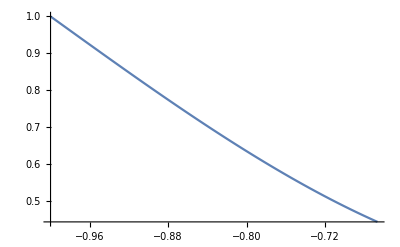
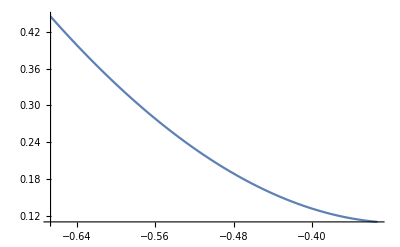
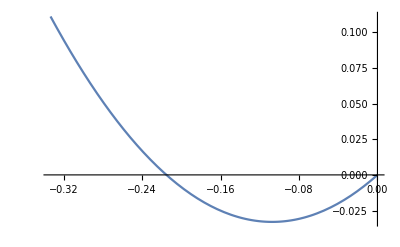
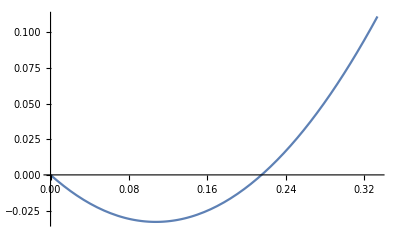
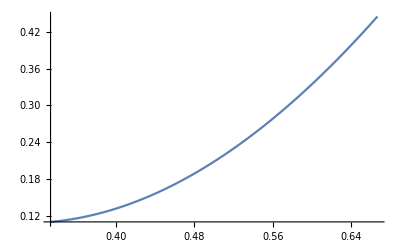
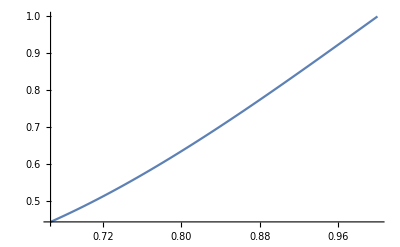
Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦j⟧,{j,1,6,1}]

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
list1 = ReadList["uniform.txt", Number, RecordLists->True];
list2 = ReadList["chebysh.txt", Number, RecordLists->True];
uni = Partition[Riffle[list1[[1]], list1[[2]]], 2];
cheb = Partition[Riffle[list2[[1]], list2[[2]]], 2];
list3= ReadList["spline.txt", Number, RecordLists->True];
n=7;
listplot={};
For[i=1,i<n,i++,
spline=list3[[i,1]]+list3[[i,2]]*(x-list1[[1,i]])+list3[[i,3]]*(x-list1[[1,i]])^2+list3[[i,4]]*(x-list1[[1,i]])^3;
listplot=Append[listplot,Plot[spline==0,{x,list1[[1,i]],list1[[1,i+1]]}]];
]
Show[listplot[[j]]]
```